# Ph20 Homework 6 Philip Carr Friday Section

Note: use ToExpression[“expression”, TeXForm] to convert LATEX syntax into Mathematica syntax.

## Part 1

Proving that the optimal firing angle is 45 degrees.

Without drag, the equations of positions x and y are

x==t v_x0+x_0

y==-(g t^2)/2+t v_y0+y_0

Here, x0 = y0 = 0. The time at which the projectile has y = 0 is when the projectile is first launched and then when the projectile lands after being launched. The time at which the projectile lands is

```mathematica
Solve[{-g t^2/2+t v0y==0,t≠0},t]
```

{{t→(2 v0y)/g}}

Thus, the value of horizontal distance the projectile travels when the projectile lands is x = (2 v0y / g) vx0. Given that vx0 = v0 cos(theta) and v0y = v0 sin(theta), where theta is the launch angle, x = 2 (v0)^2 cos(theta) sin(theta) / g = (v0)^2 sin(2 theta) / g. Taking the derivative of both sides with respect to theta, dx/d(theta) = 2 (v0)^2 cos(2 theta) / g. Setting dx/d(theta) = 0, the equation becomes 2 (v0)^2 cos(2 theta) / g = 0, which implies that cos(2 theta) = 0, which implies that
2 theta = pi / 2, thus making theta = pi / 4 = 45 degrees. Since dx/d(theta) > 0 for angles smaller than 45 degrees and since dx/d(theta) < 0 for angles larger than 45 degrees, the optimal (for maximum horizontal distance) firing angle is 45 degrees.
To launch a projectile from Caltech to PCC, over a horizontal distance of ~1000m, x = (v0)^2 sin(2 theta) / g = 1000, which implies that v0 = sqrt(1000 g / sin(2 theta)). Given that theta = 45 degrees, v0 = sqrt[1000 g] = 99.0454 m/s.

## Part 2

```mathematica
g=9.81
v0=Sqrt[1000g]
eqs={x''[t]==0,y''[t]==-g}
ini1={x[0]==0,y[0]==0,x'[0]==v0 Cos[π/6],y'[0]==v0 Sin[π/6]}
ini2={x[0]==0,y[0]==0,x'[0]==v0 Cos[π/5],y'[0]==v0 Sin[π/5]}
ini3={x[0]==0,y[0]==0,x'[0]==v0 Cos[π/4],y'[0]==v0 Sin[π/4]}
ini4={x[0]==0,y[0]==0,x'[0]==v0 Cos[π/3],y'[0]==v0 Sin[π/3]}
ini5={x[0]==0,y[0]==0,x'[0]==v0 Cos[π/2.5],y'[0]==v0 Sin[π/2.5]}
tend1=2(v0 Sin[π/6])/g
tend2=2(v0 Sin[π/5])/g
tend3=2(v0 Sin[π/4])/g
tend4=2(v0 Sin[π/3])/g
tend5=2(v0 Sin[π/2.5])/g
```

9.81

99.0454

{x''[t]==0,y''[t]==-9.81}

{x[0]==0,y[0]==0,x'[0]==85.7759,y'[0]==49.5227}

{x[0]==0,y[0]==0,x'[0]==80.1294,y'[0]==58.2175}

{x[0]==0,y[0]==0,x'[0]==70.0357,y'[0]==70.0357}

{x[0]==0,y[0]==0,x'[0]==49.5227,y'[0]==85.7759}

{x[0]==0,y[0]==0,x'[0]==30.6067,y'[0]==94.1978}

10.0964

11.869

14.2784

17.4874

19.2044

```mathematica
rules1=NDSolve[Join[eqs,ini1],{x,y},{t,0,tend1}]
rules2=NDSolve[Join[eqs,ini2],{x,y},{t,0,tend2}]
rules3=NDSolve[Join[eqs,ini3],{x,y},{t,0,tend3}]
rules4=NDSolve[Join[eqs,ini4],{x,y},{t,0,tend4}]
rules5=NDSolve[Join[eqs,ini5],{x,y},{t,0,tend5}]
```

{{x→InterpolatingFunction[{{0., 10.0964}}, <>],y→InterpolatingFunction[{{0., 10.0964}}, <>]}}

{{x→InterpolatingFunction[{{0., 11.869}}, <>],y→InterpolatingFunction[{{0., 11.869}}, <>]}}

{{x→InterpolatingFunction[{{0., 14.2784}}, <>],y→InterpolatingFunction[{{0., 14.2784}}, <>]}}

{{x→InterpolatingFunction[{{0., 17.4874}}, <>],y→InterpolatingFunction[{{0., 17.4874}}, <>]}}

{{x→InterpolatingFunction[{{0., 19.2044}}, <>],y→InterpolatingFunction[{{0., 19.2044}}, <>]}}

```mathematica
xx1[t_]:=x[t]/.rules1[[1]]
xx2[t_]:=x[t]/.rules2[[1]]
xx3[t_]:=x[t]/.rules3[[1]]
xx4[t_]:=x[t]/.rules4[[1]]
xx5[t_]:=x[t]/.rules5[[1]]

yy1[t_]:=y[t]/.rules1[[1]]
yy2[t_]:=y[t]/.rules2[[1]]
yy3[t_]:=y[t]/.rules3[[1]]
yy4[t_]:=y[t]/.rules4[[1]]
yy5[t_]:=y[t]/.rules5[[1]]
```

```mathematica
{tend1,tend2,tend3,tend4,tend5}
```

{10.0964,11.869,14.2784,17.4874,19.2044}

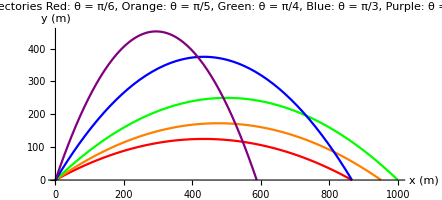

```mathematica
Show[{ParametricPlot[{xx1[t],yy1[t]},{t,0,tend1},PlotStyle->Red,PlotLabel->"Trajectories\nRed: θ = π/6, Orange: θ = π/5, Green: θ = π/4,\n Blue: θ = π/3, Purple: θ = 2π/5"],ParametricPlot[{xx2[t],yy2[t]},{t,0,tend2},PlotStyle->Orange],ParametricPlot[{xx3[t],yy3[t]},{t,0,tend3},PlotStyle->Green],ParametricPlot[{xx4[t],yy4[t]},{t,0,tend4},PlotStyle->Blue],ParametricPlot[{xx5[t],yy5[t]},{t,0,tend5},PlotStyle->Purple]},PlotRange->All,AxesLabel->{HoldForm["x (m)"],HoldForm["y (m)"]}]
```

As shown above, the trajectory of the green curve shows that the projectile launched at a 45-degree angle lands at a distance of 1000 m away from the origin.

## Part 3

```mathematica
m=0.5
r=0.05
ρ=1.3
A[r_]:=r^2/2
v0=Sqrt[1000 g]
CosTheta=Cos[π/4]
SinTheta=Sin[π/4]
```

0.5

0.05

1.3

99.0454

1/(√2)

1/(√2)

```mathematica
eqs={x''[t]==-(ρ A[r]((x'[t])^2+(y'[t])^2)/m)(x'[t]/Sqrt[(x'[t])^2+(y'[t])^2]),y''[t]==-g-(ρ A[r]((x'[t])^2+(y'[t])^2)/m)(y'[t]/Sqrt[(x'[t])^2+(y'[t])^2])}
ini={x[0]==0,y[0]==0,x'[0]==v0 CosTheta,y'[0]==v0 SinTheta}
```

{x''[t]==-0.00325 x'[t] √(x'[t]^2+y'[t]^2),y''[t]==-9.81-0.00325 y'[t] √(x'[t]^2+y'[t]^2)}

{x[0]==0,y[0]==0,x'[0]==70.0357,y'[0]==70.0357}

```mathematica
rules=NDSolve[Join[eqs,ini],{x,y},{t,0,20}]
```

{{x→InterpolatingFunction[{{0., 20.}}, <>],y→InterpolatingFunction[{{0., 20.}}, <>]}}

```mathematica
xx[t_]:=x[t]/.rules[[1]]
yy[t_]:=y[t]/.rules[[1]]
```

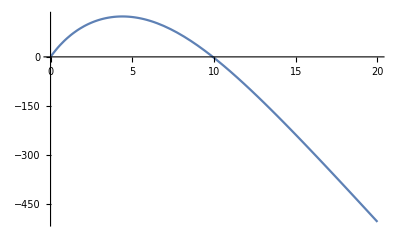

```mathematica
Plot[yy[t],{t,0,20}]
```

Solving for yy[t] = 0:

```mathematica
Solve[yy[t]==0,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-0.0000490661}}

Solving for yy[t] = 0 using another method:

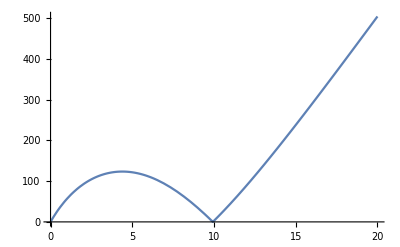

```mathematica
Plot[Abs[yy[t]],{t,0,20}]
```

```mathematica
FindMinimum[Abs[yy[t]],{t,14}]
tend=t/.FindMinimum[Abs[yy[t]],{t,14}][[2]]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{2.5856×10^-9,{t→9.92851}}

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

9.92851

Thus, yy[t] = 0 when t = tend. The distance the projectile travels a total distance of xx[tend].

```mathematica
distance=xx[tend]
```

333.33

Thus, the projectile is predicted to travel 333.33 m (with air resistance).

## Part 4

0.5

0.05

1.3

800

π/6

(√3)/2

1/2

{x''[t]==-0.00325 x'[t] √(x'[t]^2+y'[t]^2),y''[t]==-9.81-0.00325 y'[t] √(x'[t]^2+y'[t]^2)}

{x[0]==0,y[0]==0,x'[0]==400 √3,y'[0]==400}

{{x→InterpolatingFunction[{{0., 20.}}, <>],y→InterpolatingFunction[{{0., 20.}}, <>]}}

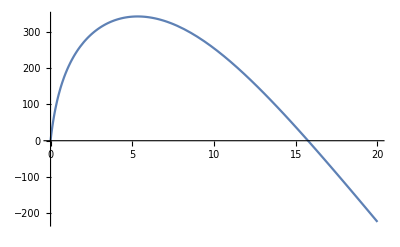

FindMinimum::fmdig: Working precision MachinePrecision is insufficient to achieve the requested accuracy or precision.

{5.94669×10^-6,{t→15.7532}}

FindMinimum::fmdig: Working precision MachinePrecision is insufficient to achieve the requested accuracy or precision.

15.7532

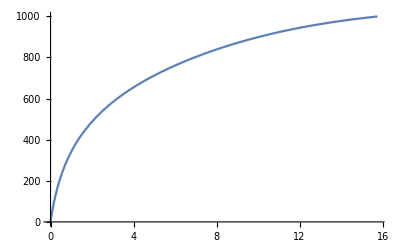

```mathematica
m=0.5
r=0.05
ρ=1.3
A[r_]:=r^2/2
v0=800
theta1=π/6
CosTheta1=Cos[theta1]
SinTheta1=Sin[theta1]
eqs={x''[t]==-(ρ A[r]((x'[t])^2+(y'[t])^2)/m)(x'[t]/Sqrt[(x'[t])^2+(y'[t])^2]),y''[t]==-g-(ρ A[r]((x'[t])^2+(y'[t])^2)/m)(y'[t]/Sqrt[(x'[t])^2+(y'[t])^2])}
ini1={x[0]==0,y[0]==0,x'[0]==v0 CosTheta1,y'[0]==v0 SinTheta1}
rules1=NDSolve[Join[eqs,ini1],{x,y},{t,0,20}]
xx1[t_]:=x[t]/.rules1[[1]]
yy1[t_]:=y[t]/.rules1[[1]]
Plot[yy1[t],{t,0,20}]
FindMinimum[Abs[yy1[t]],{t,12}]
tend1=t/.FindMinimum[Abs[yy1[t]],{t,12}][[2]]
Plot[xx1[t],{t,0,tend1}]
```

π/8

Cos[π/8]

Sin[π/8]

{x[0]==0,y[0]==0,x'[0]==800 Cos[π/8],y'[0]==800 Sin[π/8]}

{{x→InterpolatingFunction[{{0., 20.}}, <>],y→InterpolatingFunction[{{0., 20.}}, <>]}}

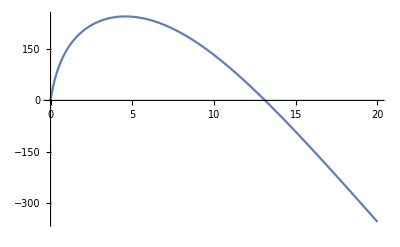

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{2.55702×10^-6,{t→13.1226}}

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

13.1226

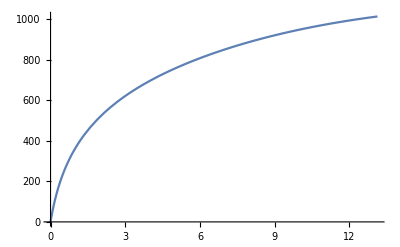

1012.79

```mathematica
theta2=π/8
CosTheta2=Cos[theta2]
SinTheta2=Sin[theta2]
ini2={x[0]==0,y[0]==0,x'[0]==v0 CosTheta2,y'[0]==v0 SinTheta2}
rules2=NDSolve[Join[eqs,ini2],{x,y},{t,0,20}]
xx2[t_]:=x[t]/.rules2[[1]]
yy2[t_]:=y[t]/.rules2[[1]]
Plot[yy2[t],{t,0,20}]
FindMinimum[Abs[yy2[t]],{t,20}]
tend2=t/.FindMinimum[Abs[yy2[t]],{t,20}][[2]]
Plot[xx2[t],{t,0,tend2}]
xx2[tend2]
```

π/10

√(5/8+(√5)/8)

1/4 (-1+√5)

{x[0]==0,y[0]==0,x'[0]==800 √(5/8+(√5)/8),y'[0]==200 (-1+√5)}

{{x→InterpolatingFunction[{{0., 14.}}, <>],y→InterpolatingFunction[{{0., 14.}}, <>]}}

InterpolatingFunction::dmval: Input value {15.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{9.31416×10^-7,{t→11.4028}}

InterpolatingFunction::dmval: Input value {15.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

11.4028

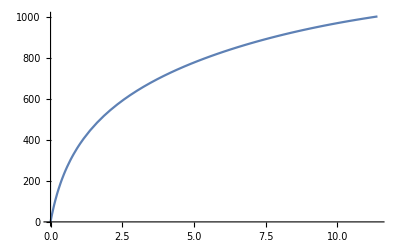

```mathematica
theta3=π/10
CosTheta3=Cos[theta3]
SinTheta3=Sin[theta3]
ini3={x[0]==0,y[0]==0,x'[0]==v0 CosTheta3,y'[0]==v0 SinTheta3}
rules3=NDSolve[Join[eqs,ini3],{x,y},{t,0,14}]
xx3[t_]:=x[t]/.rules3[[1]]
yy3[t_]:=y[t]/.rules3[[1]]
FindMinimum[Abs[yy3[t]],{t,10}]
tend3=t/.FindMinimum[Abs[yy3[t]],{t,10}][[2]]
Plot[xx3[t],{t,0,tend3}]
```

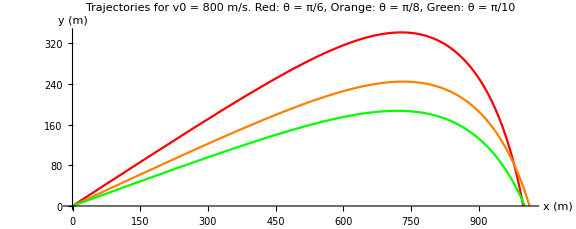

```mathematica
Show[{ParametricPlot[{xx1[t],yy1[t]},{t,0,tend1},PlotStyle->Red,PlotLabel->"Trajectories for v0 = 800 m/s. \nRed: θ = π/6, Orange: θ = π/8, Green: θ = π/10"],ParametricPlot[{xx2[t],yy2[t]},{t,0,tend2},PlotStyle->Orange],ParametricPlot[{xx3[t],yy3[t]},{t,0,tend3},PlotStyle->Green]},PlotRange->All,AxesLabel->{HoldForm["x (m)"],HoldForm["y (m)"]},ImageSize->Large]
```

As shown above, a projectile launched at a given speed achieves the greatest distance at a launch angle of approximately θ = π/8 = 22.5 degrees.

## Part 5

### (a)

```mathematica
g=9.81
m=0.5
r=0.05
ρ=1.3
A[r_]:=r^2/2
eqs={x''[t]==-(ρ A[r]((x'[t])^2+(y'[t])^2)/m)(x'[t]/Sqrt[(x'[t])^2+(y'[t])^2]),y''[t]==-g-(ρ A[r]((x'[t])^2+(y'[t])^2)/m)(y'[t]/Sqrt[(x'[t])^2+(y'[t])^2])}
```

9.81

0.5

0.05

1.3

{x''[t]==-0.00325 x'[t] √(x'[t]^2+y'[t]^2),y''[t]==-9.81-0.00325 y'[t] √(x'[t]^2+y'[t]^2)}

```mathematica
ini[θ_,v0_]:={x[0]==0,y[0]==0,x'[0]==v0 Cos[θ],y'[0]==v0 Sin[θ]}
rules[θ_,v0_]:=NDSolve[Join[eqs,ini[θ,v0]],{x,y},{t,0,20}]
yy[t_,θ_,v0_]:=y[t]/.rules[θ,v0][[1]]
landingTime[θ_,v0_]:=t/.FindMinimum[Abs[yy[t,θ,v0]],{t,20}][[2]]
```

### (b)

```mathematica
xx[t_,θ_,v0_]:=x[t]/.rules[θ,v0][[1]]
range[θ_,v0_]:=xx[landingTime[θ,v0],θ,v0]
```

```mathematica
range[π/8,8]
```

InterpolatingFunction::dmval: Input value {-144.332} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

4.56609

### (c)

```mathematica
initialVelocity[targetRange_,angle_]:=Module[{v=10},
While[targetRange-range[angle,v]>10,v=v+If[targetRange-range[angle,v]>100,100,10]];
v
]
```

### (d)

```mathematica
optimalAngle[targetRange_]:=Module[{θ=0.05},
While[initialVelocity[targetRange, θ+0.01]-initialVelocity[targetRange, θ]>100,θ=θ+0.01];
θ
]
```

```mathematica
optimalAngle[1000]
```

InterpolatingFunction::dmval: Input value {-155.482} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMinimum::fmdig: Working precision MachinePrecision is insufficient to achieve the requested accuracy or precision.

General::stop: Further output of FindMinimum::fmdig will be suppressed during this calculation.

0.06